```mathematica
Clear[f,g,h]
```

```mathematica
f[t_]:=t^2/(t^2+t+2)
```

```mathematica
g[x_]:=∫_0^x f[t]ⅆt
```

```mathematica
Solve[f[x]==0,x]
```

{{x→0},{x→0}}

```mathematica
Solve[f'[x]==0,x]
```

{{x→-4},{x→0}}

```mathematica
f'[-5]//N
```

0.0103306

```mathematica
f'[-3]//N
```

-0.046875

```mathematica
f'[1]//N
```

0.3125

```mathematica
Table[{x,g[x]},{x,-5,5}]
```

{{-5,-5+(3 ArcTan[1/(√7)])/(√7)+(3 ArcTan[9/(√7)])/(√7)-Log[11]/2},{-4,-4+(3 π)/(2 √7)-Log[7]/2},{-3,-3+(3 ArcTan[1/(√7)])/(√7)+(3 ArcTan[5/(√7)])/(√7)-Log[2]},{-2,-2+(3 ArcTan[1/(√7)])/(√7)+(3 ArcTan[3/(√7)])/(√7)-Log[2]/2},{-1,-1+(6 ArcTan[1/(√7)])/(√7)},{0,0},{1,1+(3 ArcTan[1/(√7)])/(√7)-(3 ArcTan[3/(√7)])/(√7)-Log[2]/2},{2,2+(3 ArcTan[1/(√7)])/(√7)-(3 ArcTan[5/(√7)])/(√7)-Log[2]},{3,3+(3 ArcTan[1/(√7)])/(√7)-(3 ArcTan[√7])/(√7)-Log[7]/2},{4,4+(3 ArcTan[1/(√7)])/(√7)-(3 ArcTan[9/(√7)])/(√7)-Log[11]/2},{5,5+(3 ArcTan[1/(√7)])/(√7)-(3 ArcTan[11/(√7)])/(√7)-Log[4]}}

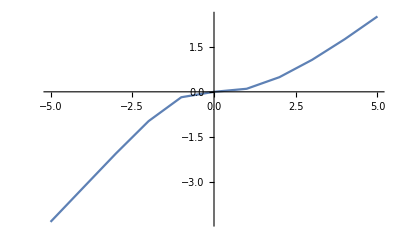

```mathematica
ListPlot[%133,Joined->True]
```

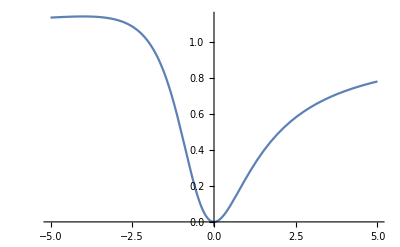

```mathematica
Plot[f[x],{x,-5,5}]
```

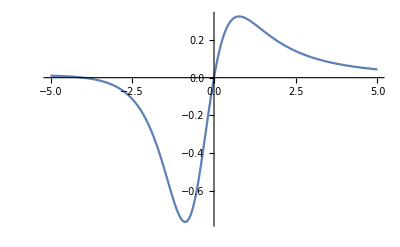

```mathematica
Plot[f'[x],{x,-5,5}]
```